```mathematica
DataStatistic[x_List]:=Module[{mean,tValue=1.14,deltaB=0.00095,uncertainty},MeanStandardDeviation[data_]:=StandardDeviation[data]/Sqrt[Length[data]];
DeltaA[data_,t_]:=t*StandardDeviation[data];
Uncertainty[data_,t_,deltaB_]:=Sqrt[DeltaA[data,t]^2+deltaB^2];mean=Mean[x];
uncertainty=Uncertainty[x,tValue,deltaB];
Print["Mean: ",mean];
Print["Standard Deviation: ",StandardDeviation[x]];
Print["Mean Standard Deviation: ",MeanStandardDeviation[x]];
Print["deltaA: ",DeltaA[x,tValue]];
Print["deltaB: ",deltaB];
Print["Uncertainty: ",uncertainty];
Return[Around[mean,uncertainty]]];

ShowFitPlot[dataX_List,dataY_List,xName_,yName_,plotName_]:=Module[{data,fitModel},data=Transpose[{dataX,dataY}];
fitModel=LinearModelFit[data,x,x];
Print["Best Fit Equation: ",fitModel["BestFit"]];
Print[Show[ListPlot[data,PlotStyle->Red,PlotLabel->plotName,AxesLabel->{xName,yName}],Plot[fitModel[x],{x,Min[dataX],Max[dataX]}]]];
Return[fitModel["BestFitParameters"]]];
ShowFitPlot[dataX_List,dataY_List,xName_,yName_]:=ShowFitPlot[dataX,dataY,xName,yName,""];
ShowFitPlot[dataX_List,dataY_List]:=ShowFitPlot[dataX,dataY,"","",""];
```

```mathematica
dataT1={7,6,6,2,1}*0.001+2.380
```

{2.387,2.386,2.386,2.382,2.381}

```mathematica
dataT2={-2,1,0,4,5}*0.001+2.540
```

{2.538,2.541,2.54,2.544,2.545}

```mathematica
dataT3={12,16,2,10,6}*0.001+2.700
```

{2.712,2.716,2.702,2.71,2.706}

```mathematica
dataT4={9,5,5,5,3}*0.001+2.850
```

{2.859,2.855,2.855,2.855,2.853}

```mathematica
dataT5={10,5,11,4,5}*0.001+2.980
```

{2.99,2.985,2.991,2.984,2.985}

```mathematica
dataT6={15,4,9,2,10}*0.001+3.110
```

{3.125,3.114,3.119,3.112,3.12}

```mathematica
T1=DataStatistic[dataT1]
```

Mean: 2.3844

Standard Deviation: 0.00270185

Mean Standard Deviation: 0.0012083

deltaA: 0.00308011

deltaB: 0.00095

Uncertainty: 0.00322329

2.38440.0032

```mathematica
T2=DataStatistic[dataT2]
```

Mean: 2.5416

Standard Deviation: 0.00288097

Mean Standard Deviation: 0.00128841

deltaA: 0.00328431

deltaB: 0.00095

Uncertainty: 0.00341894

2.54160.0034

```mathematica
T3=DataStatistic[dataT3]
```

Mean: 2.7092

Standard Deviation: 0.0054037

Mean Standard Deviation: 0.00241661

deltaA: 0.00616022

deltaB: 0.00095

Uncertainty: 0.00623304

2.7090.006

```mathematica
T4=DataStatistic[dataT4]
```

Mean: 2.8554

Standard Deviation: 0.00219089

Mean Standard Deviation: 0.000979796

deltaA: 0.00249761

deltaB: 0.00095

Uncertainty: 0.00267219

2.85540.0027

```mathematica
T5=DataStatistic[dataT5]
```

Mean: 2.987

Standard Deviation: 0.00324037

Mean Standard Deviation: 0.00144914

deltaA: 0.00369402

deltaB: 0.00095

Uncertainty: 0.00381422

2.9870.004

```mathematica
T6=DataStatistic[dataT6]
```

Mean: 3.118

Standard Deviation: 0.00514782

Mean Standard Deviation: 0.00230217

deltaA: 0.00586851

deltaB: 0.00095

Uncertainty: 0.00594491

3.1180.006

```mathematica
L=({35,40,45,50,55,60}+1.992/2)/100
```

{0.35996,0.40996,0.45996,0.50996,0.55996,0.60996}

Best Fit Equation: -0.0499542+4.08167 x

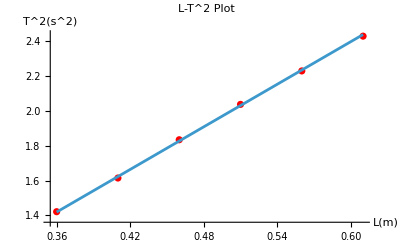

4.08167

```mathematica
k=ShowFitPlot[L,({T1,T2,T3,T4,T5,T6}/2)^2,"L(m)","T^2(s^2)","L-T^2 Plot"][[2]]
```

```mathematica
g2=(4Pi^2)/k
```

9.67211

```mathematica
dataT10={13.040,12.956,13.056,12.985,13.035}
```

{13.04,12.956,13.056,12.985,13.035}

```mathematica
dataT15={15.937,15.952,15.937,15.939,15.961}
```

{15.937,15.952,15.937,15.939,15.961}

```mathematica
dataT20={17.471,17.452,17.473,17.453,17.444}
```

{17.471,17.452,17.473,17.453,17.444}

```mathematica
T10=DataStatistic[dataT10]
```

Mean: 13.0144

Standard Deviation: 0.0420868

Mean Standard Deviation: 0.0188218

deltaA: 0.047979

deltaB: 0.00095

Uncertainty: 0.0479884

13.010.05

```mathematica
T15=DataStatistic[dataT15]
```

Mean: 15.9452

Standard Deviation: 0.0108259

Mean Standard Deviation: 0.00484149

deltaA: 0.0123415

deltaB: 0.00095

Uncertainty: 0.012378

15.9450.012

```mathematica
T20=DataStatistic[dataT20]
```

Mean: 17.4586

Standard Deviation: 0.0127397

Mean Standard Deviation: 0.00569737

deltaA: 0.0145233

deltaB: 0.00095

Uncertainty: 0.0145543

17.4590.015

Best Fit Equation: -0.0256501+3.98514 x

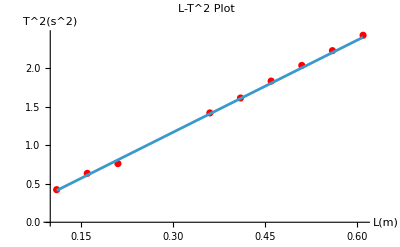

3.98514

```mathematica
k3=ShowFitPlot[({10,15,20,35,40,45,50,55,60}+1.992/2)/100,{{T10,T15,T20}/20,{T1,T2,T3,T4,T5,T6}/2}^2//Flatten,"L(m)","T^2(s^2)","L-T^2 Plot"][[2]]
```

```mathematica
g3=(4Pi^2)/k3
```

9.90641